```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
dat1=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P3/h2chain.tsv","Table"]//Flatten;
```

```mathematica
dattr=Transpose[{Range[0.75,4,0.25],dat1}];
```

```mathematica
fnfit=Interpolation[dattr,Method->"Spline",InterpolationOrder->6]
```

InterpolatingFunction[…]

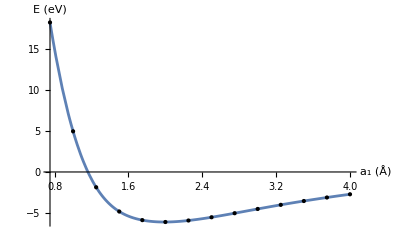

```mathematica
plt=Plot[fnfit[x],{x,0.75,4},Epilog->{Point[dattr]},PlotRange->All,AxesLabel->{"a_1 (Å)","E (eV)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/freeenplt.pdf",plt]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/freeenplt.pdf

```mathematica
FindMinimum[fnfit[x],{x,2.0}]
```

{-6.08862,{x→1.98958}}

```mathematica
dat2=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P3/h2chainK.tsv","Table"]//Flatten;
```

```mathematica
dattr2=Transpose[{Range[1,30,1],dat2}];
```

```mathematica
fnfit2=Interpolation[dattr2,Method->"Spline",InterpolationOrder->6]
```

InterpolatingFunction[…]

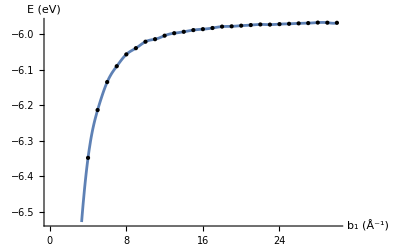

```mathematica
plt2=Plot[fnfit2[x],{x,0,30},Epilog->{Point[dattr2]},PlotRange->Automatic,AxesLabel->{"b_1 (Å^-1)","E (eV)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/freeenpltK.pdf",plt2]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/freeenpltK.pdf

```mathematica
Abs@Differences[dat2]
kpltConv=%//ListLinePlot[#,PlotRange->{0,0.01},AxesLabel->{"b_1 (Å^-1)","E (eV)"}]&;
```

{4.71631,0.872568,0.305788,0.134628,0.0787777,0.0445776,0.0332636,0.0175058,0.0182316,0.00705861,0.00992439,0.00692276,0.00400124,0.00475191,0.00263393,0.00322108,0.00398469,0.00076236,0.00183633,0.00172384,0.00170461,0.00042291,0.00132122,0.00095028,0.00119881,0.000751,0.00148379,0.00030948,0.00031685}

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/kpltConv.pdf",kpltConv]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/kpltConv.pdf

```mathematica
Around[1.9895,0.1 1.9895]
```

1.990.20

```mathematica
Range[1.99-0.2,1.99+0.2,0.0234]
```

{1.79,1.8134,1.8368,1.8602,1.8836,1.907,1.9304,1.9538,1.9772,2.0006,2.024,2.0474,2.0708,2.0942,2.1176,2.141,2.1644,2.1878}

```mathematica
0.4/17
```

0.0235294

```mathematica
dat3=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P3/setDetots.tsv","Table"]//Flatten;
```

```mathematica
dattr3=Transpose[{Range[1.79, 2.188,0.0234],dat3}];
```

```mathematica
fnfit3=Interpolation[dattr3,Method->"Spline",InterpolationOrder->6]
```

InterpolatingFunction[…]

```mathematica
fit=Fit[Take[dattr3,{3,-4}],{1,x,x^2},x]
```

8.33897-14.2221 x+3.5325 x^2

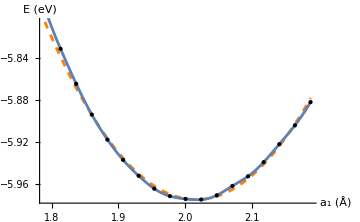

```mathematica
plt3=Show[Plot[fit,{x,1.79,2.188},ImageSize->Medium,Epilog->{Point[#]&/@dattr3},PlotRange->Full,PlotStyle->{Orange,Dashed},AxesLabel->{"a_1 (Å)","E (eV)"}],Plot[fnfit3[x],{x,1.79,2.188},PlotRange->Full,PlotLabel->""]]
```

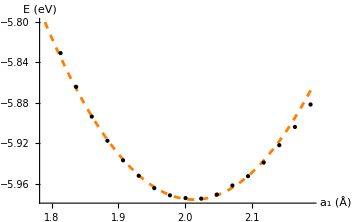

```mathematica
plt3=Plot[fit,{x,1.79,2.188},ImageSize->Medium,Epilog->{Point[#]&/@dattr3},PlotRange->All,PlotStyle->{Orange,Dashed},AxesLabel->{"a_1 (Å)","E (eV)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/fitplt3.pdf",plt3]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/fitplt3.pdf

```mathematica
Minimize[fit,x]
```

{-5.97483,{x→2.0166}}

```mathematica
dat4=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P3/dvals.tsv","Table"]//Flatten;
```

```mathematica
Length@dat4
```

61

```mathematica
dattr4=Transpose[{Range[0.25,0.75 ,0.01]  2.017-2.017/2,Take[dat4,{6,-6}]}];
```

```mathematica
fnfit4=Interpolation[dattr4,Method->"Spline",InterpolationOrder->6]
```

InterpolatingFunction[…]

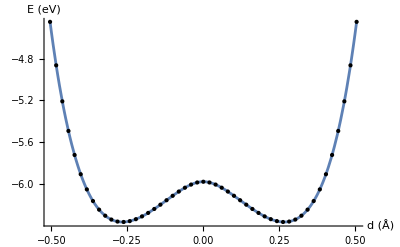

```mathematica
plt4=Plot[fnfit4[x],{x,-0.504,0.504},Epilog->{Point[dattr4]},PlotRange->Automatic,AxesLabel->{"d (Å)","E (eV)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/fitplt4.pdf",plt4]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/fitplt4.pdf

```mathematica
FindMinimum[fnfit4[x],{x,#},AccuracyGoal->4]&/@{0.7,1.3}
```

{{-6.3609,{x→0.742402}},{-6.3609,{x→1.27463}}}

```mathematica
fit4=Fit[Take[dattr4,{9,16}],{1,x,x^2},x]
```

3.21476-25.6196 x+17.133 x^2

```mathematica
FindMinimum[fit4,{x,0.7}]
```

{-6.36276,{x→0.747671}}

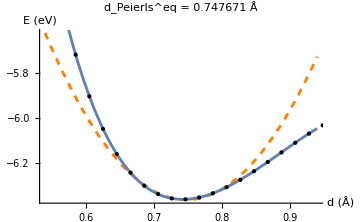

```mathematica
fitplt4=Show[Plot[fit4,{x,0.74-0.2,0.74+0.2},ImageSize->Medium,Epilog->{Point[#]&/@dattr4},PlotRange->Full,PlotStyle->{Orange,Dashed},AxesLabel->{"d (Å)","E (eV)"},PlotLabel->StringForm["d_Peierls^eq = `` Å",FindMinimum[fit4,{x,0.7}][[2]][[1]][[2]]]],Plot[fnfit4[x],{x,0.74-0.2,0.74+0.2},PlotRange->All]]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/fitplt13.pdf",fitplt4]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/fitplt13.pdf

26.7609-52.0583 x+20.4523 x^2

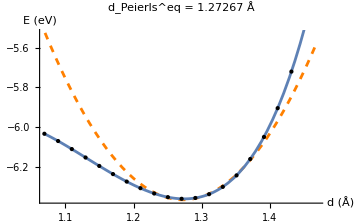

```mathematica
fit5=Fit[Take[dattr4,{37,44}],{1,x,x^2},x]
fitplt5=Show[Plot[fit5,{x,1.27-0.2,1.27+0.2},ImageSize->Medium,Epilog->{Point[#]&/@dattr4},PlotRange->Full,PlotStyle->{Orange,Dashed},AxesLabel->{"d (Å)","E (eV)"},PlotLabel->StringForm["d_Peierls^eq = `` Å",FindMinimum[fit5,{x,1.3}][[2]][[1]][[2]]]],Plot[fnfit4[x],{x,1.27-0.2,1.27+0.2},PlotRange->All]]
```

```mathematica
FindMinimum[fit5,{x,1.3}]
```

{-6.36563,{x→1.27267}}

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/fitplt5.pdf",fitplt5]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/fitplt5.pdf

```mathematica
bd=Transpose@Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P3/bands/band_``.tsv",#],"Table","HeaderLines"->1]&/@Range[1,64];
```

```mathematica
pts=Transpose[{#[[1]],#[[2]],#[[3]]}]&/@bd;
```

```mathematica
pts[[1]]//Export["~/Downloads/dat.csv",#]&
```

~/Downloads/dat.csv

```mathematica
Export[ToString@StringForm["~/Downloads/bandsData/band_``.csv",#1],#2]&@@@Transpose[{Range[1,64],pts}];
```

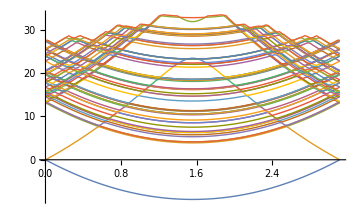

```mathematica
ptsize=Transpose[#[[3]]]&/@bd;
bddr=Transpose[{#[[1]],#[[2]]}]&/@bd
lpt=ListLinePlot[bddr,PlotStyle->Thin,ImageSize->Medium] (*Line plot*)
```

```mathematica
Export["~/Downloads/xyData.csv",dt]
```

~/Downloads/xyData.csv

```mathematica
PointSize[0.01]
ListPlot[bddr,] (*Point plot with variable size*)
```

PointSize[0.01]

ListPlot::nonopt: Options expected (instead of Null) beyond position 1 in ListPlot[{{{0.,0.},{0.02453,-0.287364},{0.04906,-0.56634},{0.07359,-0.840881},{0.09811,-1.11152},{0.12264,-1.38097},{0.14717,-1.64409},{0.1717,-1.90091},{0.19623,-2.15689},{0.22076,-2.40345},«118»},«9»,«54»},Null]. An option must be a rule or a list of rules.

```mathematica
bd[[All,{1,2,3}]]//Normal
```

```mathematica
RandomReal[1,{10,3}];
```

```mathematica
blplt=BubbleChart[pts,BubbleSizes->{0.00001, 0.01},ImageSize->Medium,Axes->True,FrameLabel->{"b_1 (Å^-1)","E (eV)"},AspectRatio->1]
```

-Graphics-

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/bands.pdf",blplt]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/bands.pdf

```mathematica
sl=Select[#,#[[3]]>0.1&]&/@pts//Flatten[#,1]&;
```

```mathematica
vsl=#[[1;;2]]&/@sl;
```

```mathematica
upb=Select[vsl,#[[2]]>=0&]//Sort//DeleteDuplicates;
```

```mathematica
db=Select[vsl,#[[2]]<=0&]//Sort//DeleteDuplicates;
```

```mathematica
ipb=Interpolation[#,InterpolationOrder->6,Method->"Spline"]&/@{db,upb}
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

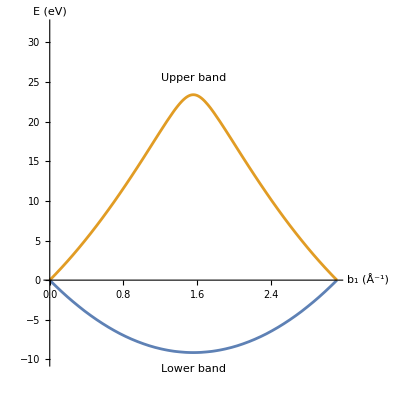

```mathematica
ppltbd=Plot[#[x]&/@ipb//Evaluate,{x,0,3.11511},PlotRange->{-10,32},AspectRatio->1,AxesLabel->{"b_1 (Å^-1)","E (eV)"},PlotLabels->{Placed["Lower band",Below],Placed["Upper band",Above]}]
```

FittedModel[20.1261 Cos[1.10063 (-1.55756+x)]]

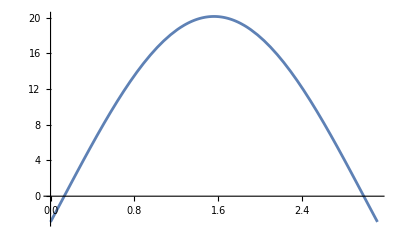

```mathematica
uf=NonlinearModelFit[upb,a Cos[k(x-x0)],{a,k,x0},x]
Plot[uf["BestFit"],{x,0,3.11511}]
```

```mathematica
Export[]
```

Export::argt: Export called with 0 arguments; 2 or 3 arguments are expected.

Export[]

```mathematica
Export["~/Downloads/upBand.csv",upb]
Export["~/Downloads/downBand.csv",db]
```

~/Downloads/upBand.csv

~/Downloads/downBand.csv

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/ppltbands.pdf",ppltbd]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/3/ppltbands.pdf